-Graphics-

# Wolfram Language

## Training 3—Programmers

-Graphics-

-Graphics-

## String Patterns

String patterns work a lot like expression patterns

String patterns can be given names and used with RuleDelayed in StringReplace and StringCases

See the String Patterns guide page for details

Many expression patterns can be used in string patterns

Sequences: __ and ___

Alternatives: "Carlo"|"Bob"|"Vitaliy"

Named: x_ and x:(…)

Qualifiers: Longest, Shortest, Except

StringExpression is the container that holds the elements of the string pattern

The infix notation is __~~__

There are several symbolic patterns

Semantic classes: Whitespace, NumberString, DatePattern

Character classes: WordCharacter, LetterCharacter, DigitCharacter, WhitespaceCharacter, PunctuationCharacter, HexadecimalCharacter

Anchors: WordBoundary, StartOfString, EndOfString

### Examples

```mathematica
(exampleData=Import["meetings.txt","Lines"])//Column
```

12:00am Bhubanjyoti Bhattacharya & Bernat
12:15am Andrey Grabovsky & Bernat
3:15pm Connor Bain & Carlo
3:30pm Jackreece Ejini & Carlo
3:45pm Daavid Vaananen & Ian
4:00pm Les Grundman & Ian
4:15pm Daniel Reynolds & Matthew
4:30pm Monica Linden & Matthew
4:45pm Leo McElroy & Matthew
5:00pm Christopher DeFiglia & Matthew
5:15pm Hikari Sorenson & Giulio
5:30pm Nae Eoun Lee & Giulio
8:30pm Sung Min Yoon & Matthew
8:45pm Ethan Truelove & Timothee
9:00pm Carlos Manual Rodriguez Martinez & Timothee
9:15pm Rohan Saxena & Matteo
9:30pm Benjamin Keller & Timothee
9:45pm Soham Pal & Timothee
10:00pm Rian Shams & Timothee
10:15pm Emilio Andres Vazquz & Bob

Let’s get the lines for Matt’s students

```mathematica
StringCases[exampleData,___~~"Matthew"~~___]
```

{{},{},{},{},{},{},{4:15pm Daniel Reynolds & Matthew},{4:30pm Monica Linden & Matthew},{4:45pm Leo McElroy & Matthew},{5:00pm Christopher DeFiglia & Matthew},{},{},{8:30pm Sung Min Yoon & Matthew},{},{},{},{},{},{},{}}

/; == if

```mathematica
Cases[exampleData,line_/;StringMatchQ[line,___~~"Matthew"~~___]]//Column
```

4:15pm Daniel Reynolds & Matthew
4:30pm Monica Linden & Matthew
4:45pm Leo McElroy & Matthew
5:00pm Christopher DeFiglia & Matthew
8:30pm Sung Min Yoon & Matthew

Who are Matt’s students?

. 1, .. one or more, ... zero or more

```mathematica
Join@@StringCases[exampleData,Except[WhitespaceCharacter]..~~" "~~student__~~" & Matthew"~~___:>student]
```

{Daniel Reynolds,Monica Linden,Leo McElroy,Christopher DeFiglia,Sung Min Yoon}

When does Matt have to be present?

```mathematica
Join@@StringCases[exampleData,StartOfString~~time__~~" "~~___~~"Matthew"~~___:>TimeObject[time]]
```

{16:15:00GMT-4.TimeObject[{16,15,0.},TimeZone→-4.],16:30:00GMT-4.TimeObject[{16,30,0.},TimeZone→-4.],16:45:00GMT-4.TimeObject[{16,45,0.},TimeZone→-4.],17:00:00GMT-4.TimeObject[{17,0,0.},TimeZone→-4.],20:30:00GMT-4.TimeObject[{20,30,0.},TimeZone→-4.]}

Let’s “translate” the lines into German

```mathematica
StringReplace[exampleData,StartOfString~~time__~~meridian:("am"|"pm")~~" "~~student__~~" & "~~instructor__~~EndOfString:>DateString[time<>meridian,{"Hour24",":","Minute"}]<>" "<>student<>" und "<>instructor]//Column
```

00:00 Bhubanjyoti Bhattacharya und Bernat
00:15 Andrey Grabovsky und Bernat
15:15 Connor Bain und Carlo
15:30 Jackreece Ejini und Carlo
15:45 Daavid Vaananen und Ian
16:00 Les Grundman und Ian
16:15 Daniel Reynolds und Matthew
16:30 Monica Linden und Matthew
16:45 Leo McElroy und Matthew
17:00 Christopher DeFiglia und Matthew
17:15 Hikari Sorenson und Giulio
17:30 Nae Eoun Lee und Giulio
20:30 Sung Min Yoon und Matthew
20:45 Ethan Truelove und Timothee
21:00 Carlos Manual Rodriguez Martinez und Timothee
21:15 Rohan Saxena und Matteo
21:30 Benjamin Keller und Timothee
21:45 Pal und Timothee
22:00 Rian Shams und Timothee
22:15 Emilio Andres Vazquz und Bob

## More on Data Processing

### Padding ragged lists

```mathematica
raggedLists={{"t","h","e"},{"q","u","i","c","k"},{"b","r","o","w","n"},{"f","o","x"},{"j","u","m","p","s"},{"o","v","e","r"},{"t","h","e"},{"l","a","z","y"},{"d","o","g"}};
```

```mathematica
Grid[raggedLists]
```

t | h | e |  | 
q | u | i | c | k
b | r | o | w | n
f | o | x |  | 
j | u | m | p | s
o | v | e | r | 
t | h | e |  | 
l | a | z | y | 
d | o | g |  |

```mathematica
?PadRight
```

PadRight[list,n] makes a list of length n by padding list with zeros on the right. 
PadRight[list,n,x] pads by repeating the element x. 
PadRight[list,n,{x_1,x_2,…}] pads by cyclically repeating the elements x_i. 
PadRight[list,n,padding,m] leaves a margin of m elements of padding on the left. 
PadRight[list,{n_1,n_2,…}] makes a nested list with length n_i at level i. 
PadRight[list] pads a ragged array list with zeros to make it full.

```mathematica
PadRight[raggedLists,Automatic,"⎵"]//Grid
```

t | h | e | ⎵ | ⎵
q | u | i | c | k
b | r | o | w | n
f | o | x | ⎵ | ⎵
j | u | m | p | s
o | v | e | r | ⎵
t | h | e | ⎵ | ⎵
l | a | z | y | ⎵
d | o | g | ⎵ | ⎵

```mathematica
PadLeft[raggedLists,Automatic,""]//Grid
```

|  | t | h | e
q | u | i | c | k
b | r | o | w | n
 |  | f | o | x
j | u | m | p | s
 | o | v | e | r
 |  | t | h | e
 | l | a | z | y
 |  | d | o | g

### Side effects

```mathematica
𝒟ℬ=Dataset[{<|"name"->"Bill","age"->32,"gender"->♂|>,<|"name"->"Alice","gender"->♀,"age"->28|>}]
```

Dataset[<>]

```mathematica
insert[record_]:=AppendTo[𝒟ℬ,record]
```

```mathematica
transactions={<|"name"->"Wan","gender"->♀|>,<|"name"->"Berta","age"->17,"gender"->♀|>,<|"name"->"Paulo","age"->27,"gender"->♂|>};
```

```mathematica
Scan[insert,transactions]
```

```mathematica
𝒟ℬ
```

Dataset[<>]

### Some useful functional paradigms

#### Thread

```mathematica
Thread[{4,{3,2,1}}]
```

{{4,3},{4,2},{4,1}}

```mathematica
Thread[{𝒳,𝒴,𝒵}->𝒜]
```

{𝒳→𝒜,𝒴→𝒜,𝒵→𝒜}

```mathematica
Thread[{α,β,γ}->{0.4102,0.4375,0.4801}]
```

{α→0.4102,β→0.4375,γ→0.4801}

```mathematica
AssociationThread[{α,β,γ}->{0.4102,0.4375,0.4801}]
```

<|α→0.4102,β→0.4375,γ→0.4801|>

#### Through

```mathematica
size=({{9, 0, 10, 2, 5, 0, 7}, {5, 3, 5, 10, 4, 0, 3}, {1, 9, 7, 6, 4, 4, 8}, {1, 6, 2, 8, 7, 10, 8}, {6, 7, 4, 7, 9, 7, 10}, {2, 10, 8, 0, 0, 4, 2}, {0, 8, 9, 5, 1, 8, 3}});
```

```mathematica
Through[{Min,Max}[size]]
```

{0,10}

#### MapThread

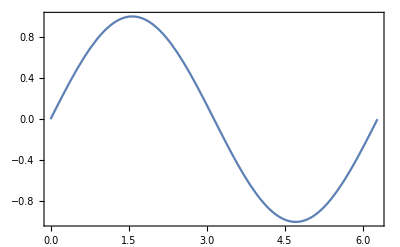
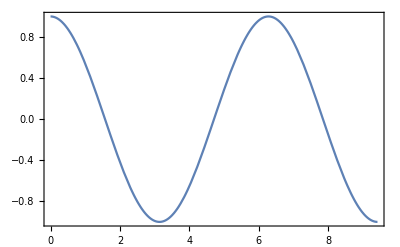
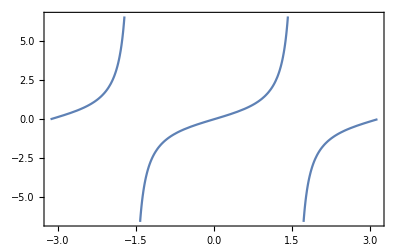

```mathematica
MapThread[Plot,{{Sin[x],Cos[y],Tan[z]},{{x,0,2π},{y,0,3π},{z,-π,π}}}]
```

Question from audience: can you show the three plots overlaid?

ColorData[97] is the color function used for the default plot theme.

```mathematica
ColorData[97] /@{1,2,3}
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885]}

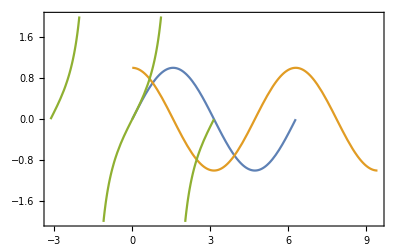

```mathematica
Show@@MapThread[Plot[#1,#2,PlotRange->{All,{-2,2}},PlotStyle->#3]&,{{Sin[x],Cos[y],Tan[z]},{{x,0,2π},{y,0,3π},{z,-π,π}},ColorData[97]/@{1,2,3}}]//Legended[#,LineLegend[ColorData[97]/@{1,2,3},{Sin[x],Cos[y],Tan[z]}]]&
```

#### ReplaceAllRepeated

```mathematica
tree={"H",{{"He",{{"Be",{}},{"B",{}},{"C",{}}}},{"Li",{{"N",{}},{"O",{{"F",{2}}}}}}}};
```

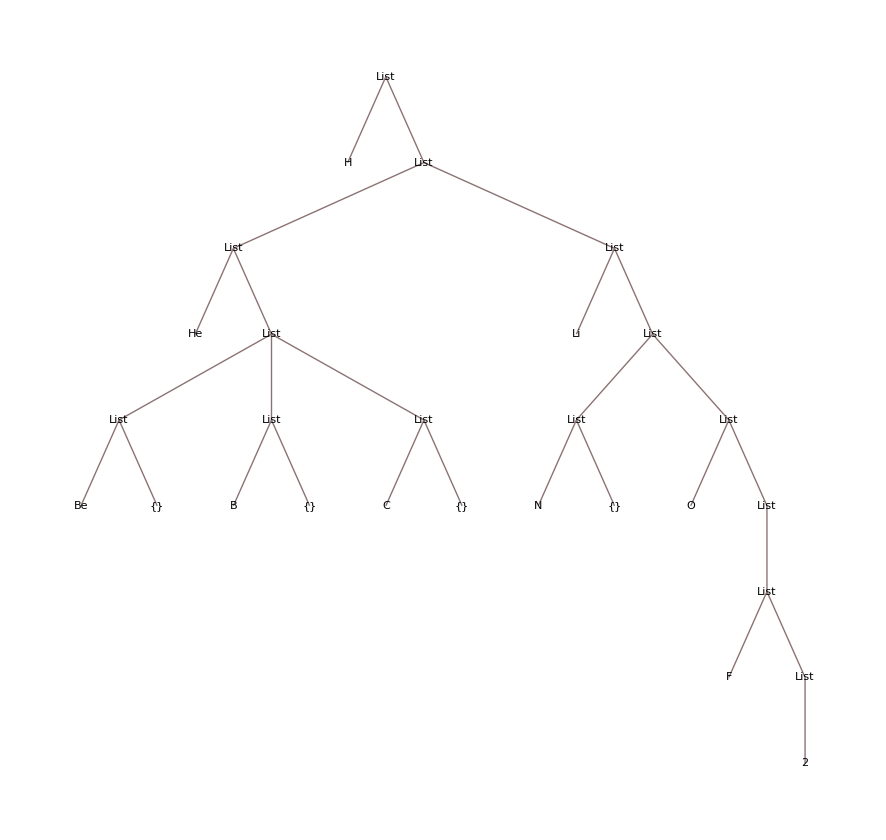

```mathematica
TreeForm[tree]
```

```mathematica
rule={root_String,branches:{___}}:>𝒯[root,branches];
```

```mathematica
tree/.rule
```

```mathematica
𝒯["H",{{"He",{{"Be",{}},{"B",{}},{"C",{}}}},{"Li",{{"N",{}},{"O",{{"F",{2}}}}}}}]
```

𝒯[H,{{He,{{Be,{}},{B,{}},{C,{}}}},{Li,{{N,{}},{O,{{F,{2}}}}}}}]

```mathematica
tree=tree//.rule
```

```mathematica
𝒯["H",{𝒯["He",{𝒯["Be",{}],𝒯["B",{}],𝒯["C",{}]}],𝒯["Li",{𝒯["N",{}],𝒯["O",{𝒯["F",{2}]}]}]}]
```

𝒯[H,{𝒯[He,{𝒯[Be,{}],𝒯[B,{}],𝒯[C,{}]}],𝒯[Li,{𝒯[N,{}],𝒯[O,{𝒯[F,{2}]}]}]}]

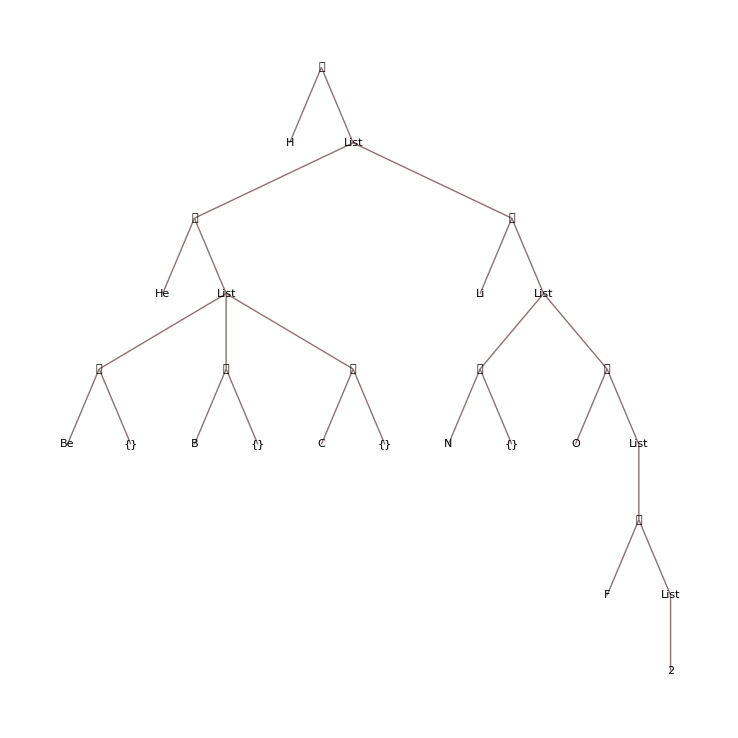

```mathematica
TreeForm[tree]
```

```mathematica
e[𝒯[r_,b_]]:=Join[r->First[#]&/@b,Join@@e/@b]
```

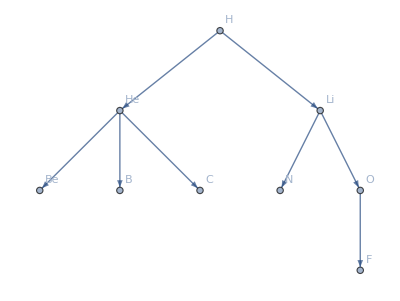

```mathematica
e[tree]//Graph[#,VertexLabels->"Name"]&
```

## Stacks, Queues, and Linked Lists

Stacks, queues, and linked lists are useful data structures

often used as components of algorithms

Wolfram Language does not have built-in forms of these structures

The package StackQueue.m implements these structures along with constructors, deconstructors, and methods

A stack uses nested Lists

A queue uses two stacks

A linked list uses DownValues (original idea from Danny Lichtblau)

```mathematica
SetDirectory[NotebookDirectory[]];
<<StackQueue`
```

StackQueue.m, $Revision: 1.7 $).
	Direct queries to Robert Nachbar, rnachbar@wolfram.com.

```mathematica
?StackQueue
```

StackQueue.m is a package that provides efficient stack and queue functions.

### Stacks

Elements are pushed onto the top of a stack

Elements are popped off the top of a stack

```mathematica
stackInfo[]
```

stackInfo[]

```mathematica
InitializeStack[𝒮]
```

```mathematica
Push[𝒮,"abc"]
```

```mathematica
Push[𝒮,123]
```

```mathematica
Push[𝒮,{5,6,7}]
```

```mathematica
PrintStack[𝒮]
```

{5,6,7}

123

abc

```mathematica
FetchStack[𝒮]
```

{abc,123,{5,6,7}}

```mathematica
Pop[𝒮]
```

{5,6,7}

```mathematica
Pop[𝒮]
```

123

```mathematica
Pop[𝒮]
```

abc

```mathematica
Pop[𝒮]
```

Pop::empty: 𝒮 has length 0 and no top element.

Pop[𝒮]

```mathematica
ClearStack[𝒮]
```

```mathematica
Pop[𝒮]
```

Pop::stack: 𝒮 is not a stack.

Pop[𝒮]

### Queues

Elements are enqueued at the back of a queue

Elements are dequeued from the front of a queue

Elements are requeued at the front of the queue (in this implementation)

```mathematica
queueInfo[]
```

```mathematica
InitializeQueue[𝒬]
```

```mathematica
Enqueue[𝒬,π]
```

```mathematica
Enqueue[𝒬,17]
```

```mathematica
Enqueue[𝒬,{"x","y","z"}]
```

```mathematica
PrintQueue[𝒬]
```

π

17

{x,y,z}

```mathematica
Dequeue[𝒬]
```

π

```mathematica
Dequeue[𝒬]
```

17

```mathematica
Dequeue[𝒬]
```

{x,y,z}

```mathematica
Dequeue[𝒬]
```

Dequeue::empty: 𝒬 has length 0 and no front element.

Dequeue[𝒬]

```mathematica
ClearQueue[𝒬]
```

```mathematica
Dequeue[𝒬]
```

Dequeue::queue: 𝒬 is not a queue.

Dequeue[𝒬]

### (Linked)Lists

Elements are inserted at the end of a linked list

Elements are never deleted from a linked list (in this implementation)

Elements of a linked list can be retrieved by position (counting from the beginning)

```mathematica
linkedListInfo[]
```

linkedListInfo[]

```mathematica
InitializeList[ℒ]
```

```mathematica
LengthList[ℒ]
```

0

```mathematica
InsertList[ℒ,π]
```

```mathematica
InsertList[ℒ,N@π]
```

```mathematica
LengthList[ℒ]
```

2

```mathematica
PartList[ℒ,1]
```

π

```mathematica
PartList[ℒ,2]
```

PartList::list: ℒ is not a list.

PartList[ℒ,2]

```mathematica
PrintList[ℒ]
```

π

3.14159

```mathematica
InsertList[ℒ,{a,b}]
InsertList[ℒ,17]
```

```mathematica
FetchList[ℒ]
```

{π,3.14159,{a,b},17}

```mathematica
ClearList[ℒ]
```

```mathematica
LengthList[ℒ]
```

LengthList::list: ℒ is not a list.

```mathematica
LengthList[ℒ]
```

LengthList[ℒ]

## Trees & Graphs for Organizing Data

```mathematica
tree
```

𝒯[H,{𝒯[He,{𝒯[Be,{}],𝒯[B,{}],𝒯[C,{}]}],𝒯[Li,{𝒯[N,{}],𝒯[O,{𝒯[F,{}]}]}]}]

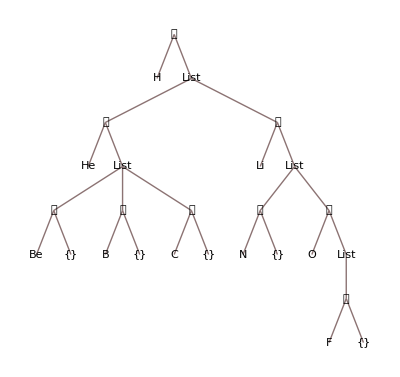

```mathematica
TreeForm[tree]
```

```mathematica
edges=Join@@Cases[tree,𝒯[r_,b:{__}]:>Thread[r->First/@b],{0,∞}]
Length@%
```

{He->Be,He->B,He->C,O->F,Li->N,Li->O,H->He,H->Li}

8

```mathematica
vertices=Union@@List@@@edges
Length@%
```

{B,Be,C,F,H,He,Li,N,O}

9

```mathematica
payLoad=#->ElementData[#,"AtomicMass"]&/@vertices
```

{B→10.81 u,Be→9.0121831 u,C→12.011 u,F→18.998403163 u,H→1.008 u,He→4.002602 u,Li→6.94 u,N→14.007 u,O→15.999 u}

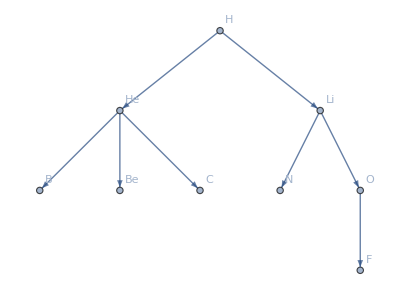

```mathematica
g=Graph[vertices,edges,VertexCapacity->payLoad,VertexLabels->Automatic]
```

```mathematica
root=FirstCase[Thread[{vertices,VertexInDegree[g]}],{r_,0}:>r]
```

H

```mathematica
First@Last@Reap@DepthFirstScan[g,root,{"PrevisitVertex"->(Sow[PropertyValue[{g,#},VertexCapacity]]&)}]
```

{1.008 u,4.002602 u,9.0121831 u,10.81 u,12.011 u,6.94 u,14.007 u,15.999 u,18.998403163 u}

```mathematica
First@Last@Reap@DepthFirstScan[g,root,{"PostvisitVertex"->(Sow[PropertyValue[{g,#},VertexCapacity]]&)}]
```

{9.0121831 u,10.81 u,12.011 u,4.002602 u,14.007 u,18.998403163 u,15.999 u,6.94 u,1.008 u}

```mathematica
First@Last@Reap@BreadthFirstScan[g,root,{"PrevisitVertex"->(Sow[PropertyValue[{g,#},VertexCapacity]]&)}]
```

{1.008 u,4.002602 u,6.94 u,9.0121831 u,10.81 u,12.011 u,14.007 u,15.999 u,18.998403163 u}

```mathematica
First@Last@Reap@BreadthFirstScan[g,root,{"PostvisitVertex"->(Sow[PropertyValue[{g,#},VertexCapacity]]&)}]
```

{1.008 u,4.002602 u,6.94 u,9.0121831 u,10.81 u,12.011 u,14.007 u,15.999 u,18.998403163 u}

## Graphs for Modeling Data

```mathematica
firms={"Macy's","Bloomingdale's","Lord & Taylor","Sam's Club","Home Depot","Walmart"};
n=Length@firms
```

6

```mathematica
assets=10^RandomReal[{4,6},{n}]
```

{178219.,73548.,16206.4,533697.,51450.8,68387.7}

```mathematica
trade=With[{t=10^RandomReal[{3,5},{n,n}]},t-DiagonalMatrix[Diagonal[t]]];
```

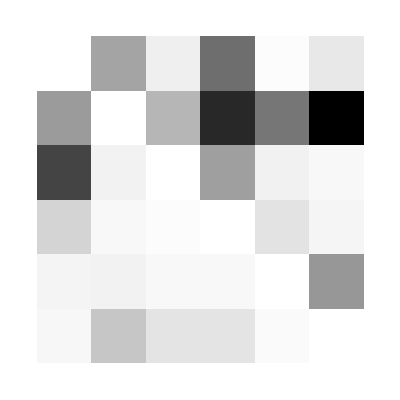

```mathematica
ArrayPlot[trade,FrameTicks->{Thread[{Range[n],firms}],Thread[{Range[n],Rotate[#,90Degree]&/@firms}]}]
```

Each row i represents the sale of goods from firm_i to the other firms

Each column j represents the  purchase of supplies by firm_j from the other firms

```mathematica
edges=Join@@MapIndexed[If[Unequal@@#2,Property[DirectedEdge@@#2,EdgeWeight->#1],Nothing]&,trade,{2}];
Short@%
```

```mathematica
{Property[1->2,EdgeWeight->31344.515619667884],«29»}
```

```mathematica
vertices=MapThread[Property[#1,{VertexCapacity->#2+#3-#4,VertexLabels->#5}]&,{Range[n],assets,Total/@trade,Total@trade,firms}];
Short@%
```

```mathematica
{Property[1,{VertexCapacity->153617.69018735006,«1»}],«4»,«1»}
```

```mathematica
Module[
{
g=Graph[vertices,edges,VertexLabels->True],vertexShape,edgeShape},

With[{max=VertexCapacity/.Rest/@List@@@vertices//Max},
vertexShape[pt_,v_,s_]:={Opacity[0.5,Blue],Disk[pt,0.25PropertyValue[{g,v},VertexCapacity]/max]}
];

With[{max=EdgeWeight/.Rest/@List@@@edges//Max},
edgeShape[pts_,e_]:={GrayLevel[0.9(max-PropertyValue[{g,e},EdgeWeight])/max],Arrow[pts]}
];

Graph[g,VertexShapeFunction->vertexShape,EdgeShapeFunction->edgeShape,PlotRangePadding->{{Scaled[0.1],Scaled[0.2]},{Scaled[0.05],Scaled[0.05]}}]
]
```

-Graphics-

## SortBy, SplitBy, GatherBy, GroupBy

### SortBy

```mathematica
data=byData[25];
Take[%,5]//TableForm
```

length | width | age | weight | cost | date
67.8 | 91.5 | 5 | 19 | 10.8 | Sun 1 Apr 2018 12:09:16GMT-4.
25.2 | 49.6 | 6 | 23 | 74.53 | Sun 1 Apr 2018 18:20:38GMT-4.
26.5 | 95.6 | 1 | 64 | 29.14 | Tue 3 Apr 2018 04:25:00GMT-4.
14.5 | 36.8 | 2 | 33 | 21.8 | Wed 4 Apr 2018 01:17:39GMT-4.

Let’s say we need to bin the data by the the “Length”

In this case Sort will work very conveniently

```mathematica
sortedData=Prepend[Sort[Rest@data],First@data];
Take[%,5]//TableForm
```

length | width | age | weight | cost | date
3.6 | 10.2 | 10 | 93 | 8.54 | Sun 15 Apr 2018 03:03:25GMT-4.
3.8 | 65.5 | 2 | 2 | 98.99 | Thu 5 Apr 2018 20:46:49GMT-4.
5.4 | 93.1 | 7 | 54 | 25.87 | Fri 20 Apr 2018 18:53:26GMT-4.
13.7 | 20.4 | 8 | 86 | 94.2 | Fri 6 Apr 2018 00:07:53GMT-4.

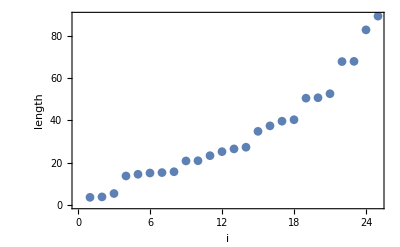

```mathematica
ListPlot[First/@Rest@sortedData,FrameLabel->{"i",First@First@sortedData}]
```

Now, let’s sort by “age”

```mathematica
?SortBy
```

SortBy[list,f] sorts the elements of list in the order defined by applying f to each of them. 
SortBy[f] represents an operator form of SortBy that can be applied to an expression.

One possible sort by function is

```mathematica
sortBy=#⟦3⟧&
```

```mathematica
#1⟦3⟧&
```

#1⟦3⟧&

However, what if the is array is very wide and we’re not sure which column is “age”? Then this function is more useful

```mathematica
sortBy=With[{p=FirstPosition[First[data],"age"]//First},#⟦p⟧&]
```

#1⟦3⟧&

```mathematica
sortedData=Prepend[SortBy[Rest@data,sortBy],First@data];
Take[%,5]//TableForm
```

length | width | age | weight | cost | date
20.9 | 11.8 | 1 | 18 | 31.4 | Fri 20 Apr 2018 03:52:12GMT-4.
26.5 | 95.6 | 1 | 64 | 29.14 | Tue 3 Apr 2018 04:25:00GMT-4.
34.8 | 4.6 | 1 | 27 | 50.56 | Mon 16 Apr 2018 16:43:33GMT-4.
52.6 | 20.4 | 1 | 70 | 94.13 | Sun 15 Apr 2018 17:44:45GMT-4.

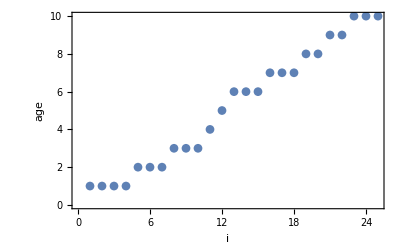

```mathematica
ListPlot[sortBy/@Rest@sortedData,FrameLabel->{"i",sortBy@First@sortedData}]
```

Now, how could we sort by area?

### SplitBy

```mathematica
?SplitBy
```

SplitBy[list,f] splits list into sublists consisting of runs of successive elements that give the same value when f is applied.
SplitBy[list,{f_1,f_2,…}] recursively splits list into sublists by testing elements successively with each of the f_i.

Let’s split the data into subsets by week

Are the data already ordered by “date”?

OK, what would the splitting function be?

### GatherBy

How could we subset the data by age?

```mathematica
?GatherBy
```

GatherBy[list,f] gathers into sublists each set of elements in list that gives the same value when f is applied.
GatherBy[list,{f_1,f_2,…}] gathers list into nested sublists using f_i at level i.

```mathematica
First@data
```

{length,width,age,weight,cost,date}

```mathematica
gatheredData=GatherBy[Rest@data,#⟦3⟧&];
Length/@%
```

{1,3,4,3,2,2,3,3,3,1}

### GroupBy

Mean on association will apply to value directly

Mean /@ GroupBy...

How would we get the average weight by age?

```mathematica
?GroupBy
```

GroupBy[{elem_1,elem_2,…},f] gives an association that groups the elem_i into lists associated with distinct keys f[elem_i].
GroupBy[{elem_1,elem_2,…},f_k→f_v] groups the f_v[elem_i] according to the f_k[elem_i].
GroupBy[{elem_1,elem_2,…},{fs_1,fs_2,…}] groups into nested associations using fs_i at level i.
GroupBy[{elem_1,elem_2,…},spec,red] applies the function red to reduce lists of values that are generated.
GroupBy[spec] represents an operator form of GroupBy that can be applied to an expression.

## Debugging

Most developers rely on instrumented code to find bugs

Unlike compiled languages, adding Print or Echo will generally not cause to code to evaluate differently

### Echo

Echo prints its input and then returns it

{2,2,9,3,5,5,1,2,10,3}

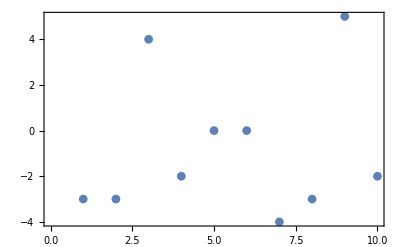

```mathematica
RandomInteger[{0,10},10]//Echo//Map[#-5&,#]&//ListPlot
```

Instrument code to follow data processing

```mathematica
munge[dataIn_]:=Module[{data=dataIn},
data=1/data;
data=3data+6;
data=1/data;
data^2
]
```

```mathematica
testData={-3/4,3/2,3/4,3/5,-1/2,-1,-3,1/2,-3/5,-1};
```

```mathematica
munge[testData]
```

Power::infy: Infinite expression 1/0 encountered.

{1/4,1/64,1/100,1/121,ComplexInfinity,1/9,1/25,1/144,1,1/9}

```mathematica
munge[dataIn_]:=Module[{data=dataIn},
data=1/data//Echo[#,"after division"]&;
data=3data+6//Echo[#,"after addition"]&;
data=1/data//Echo[#,"after second division"]&;
data^2
]
```

```mathematica
munge[testData]
```

after division 1/testData

after addition 6+3/testData

after second division 1/(6+3/testData)

1/(6+3/testData)^2

### TracePrint

```mathematica
tree
```

𝒯[H,{𝒯[He,{𝒯[Be,{}],𝒯[B,{}],𝒯[C,{}]}],𝒯[Li,{𝒯[N,{}],𝒯[O,{𝒯[F,{}]}]}]}]

```mathematica
dfsPre[𝒯[root_,branches:{___}]]:=Prepend[Join@@dfsPre/@branches,root]
dfsPost[𝒯[root_,branches:{___}]]:=Append[Join@@dfsPost/@branches,root]
```

```mathematica
TracePrint[dfsPre[tree],_dfsPre]
```

dfsPre[tree]

dfsPre[𝒯[H,{𝒯[He,{𝒯[Be,{}],𝒯[B,{}],𝒯[C,{}]}],𝒯[Li,{𝒯[N,{}],𝒯[O,{𝒯[F,{}]}]}]}]]

dfsPre[𝒯[He,{𝒯[Be,{}],𝒯[B,{}],𝒯[C,{}]}]]

dfsPre[𝒯[Be,{}]]

dfsPre[𝒯[B,{}]]

dfsPre[𝒯[C,{}]]

dfsPre[𝒯[Li,{𝒯[N,{}],𝒯[O,{𝒯[F,{}]}]}]]

dfsPre[𝒯[N,{}]]

dfsPre[𝒯[O,{𝒯[F,{}]}]]

dfsPre[𝒯[F,{}]]

{H,He,Be,B,C,Li,N,O,F}

```mathematica
TracePrint[dfsPre[tree],dfsPre[𝒯["Li",_]]]
```

dfsPre[𝒯[Li,{𝒯[N,{}],𝒯[O,{𝒯[F,{}]}]}]]

{H,He,Be,B,C,Li,N,O,F}

## Initialization

```mathematica
AppendTo[$Path,NotebookDirectory[]];
```

```mathematica
e[𝒯[r_,b_]]:=Join[r->First[#]&/@b,Join@@e/@b]
showTree[tree_]:=Graph[e[tree],VertexLabels->"Name"]
```

```mathematica
stackInfo[]:=DeleteCases[Names["StackQueue`*Stack*"|"StackQueue`Push"|"StackQueue`Pop"],"StackQueue"|(n_/;StringMatchQ[n,__~~"`Private`"~~__])]//Information[Evaluate[Alternatives@@#],LongForm->False]&
```

```mathematica
queueInfo[]:=DeleteCases[Names["StackQueue`*ueue*"],"StackQueue"|(n_/;StringMatchQ[n,__~~"`Private`"~~__])]//Information[Evaluate[Alternatives@@#],LongForm->False]&
```

```mathematica
linkedListInfo[]:=DeleteCases[Names["StackQueue`*List*"],"StackQueue"|(n_/;StringMatchQ[n,__~~"`Private`"~~__])]//Information[Evaluate[Alternatives@@#],LongForm->False]&
```

```mathematica
byData[n_]:=(SeedRandom[1234567];Module[{data=RandomReal[{0,100},{n,6}]},data⟦All,{1,2}⟧=data⟦All,{1,2}⟧//Round[#,0.1]&;data⟦All,3⟧=Ceiling[data⟦All,3⟧/10];data⟦All,4⟧=Ceiling[data⟦All,4⟧];data⟦All,5⟧=data⟦All,5⟧//Round[#,0.01]&;data⟦All,6⟧=DateObject[{2018,4,1,0,0,60 60 24 30/100#}]&/@data⟦All,6⟧;SortBy[data,Last]]//Prepend[#,{"length","width","age","weight","cost","date"}]&)
```

```mathematica
toWeekDate[date_]:=With[{ymd=DateList[date]⟦;;3⟧,dow=ToExpression@DateString[date,"ISOWeekDay"]},DateObject@DatePlus[ymd,{-dow,"Day"}]]
```

```mathematica
toWeekDate[Now]
```

Day: Sun 24 Jun 2018